```mathematica
Limit Distributions
```

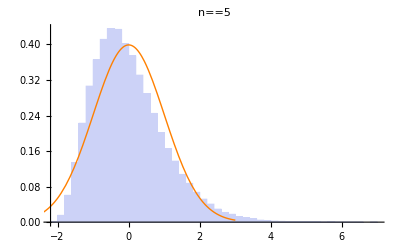
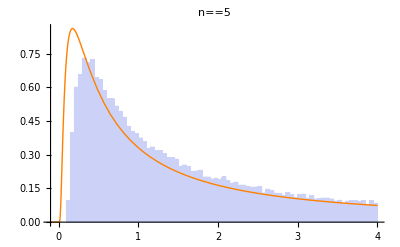
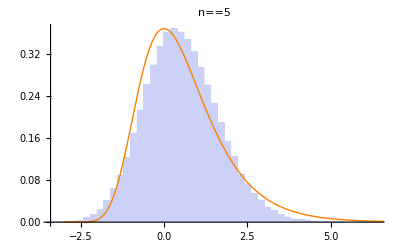
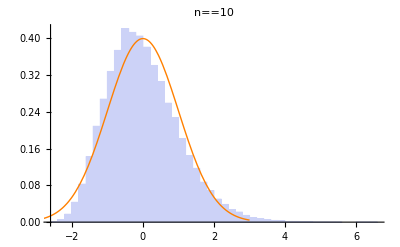
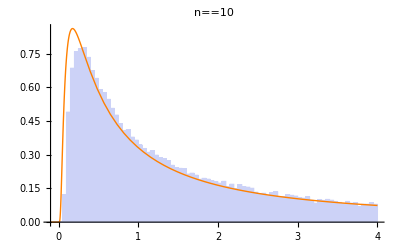
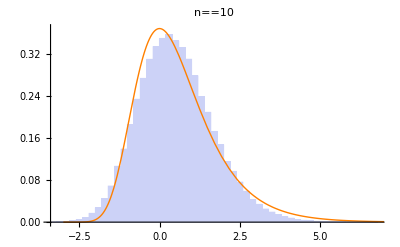
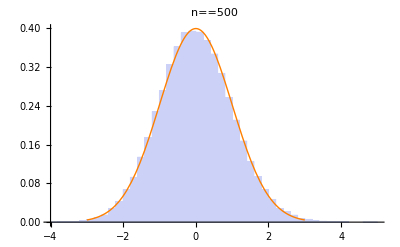
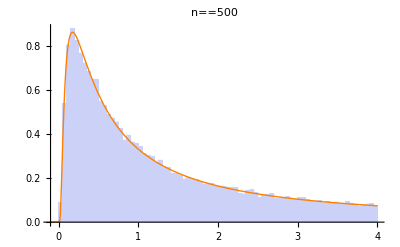
1/(√n σ)(x_1+…+x_n-μ n) | 1/n^(1/α)(x_1+…+x_n) | a_n max(x_1,…,x_n)+b_n
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
NormalDistribution | StableDistribution | MaxStableDistribution

```mathematica
clt=With[{parent𝒟=ExponentialDistribution[1]},Table[Show[Histogram[RandomVariate[TransformedDistribution[(Total[Array[x,n]]-Mean[parent𝒟] n)/(StandardDeviation[parent𝒟] Sqrt[n]),Array[x,n]\[Distributed]ProductDistribution[{parent𝒟,n}]],10^5],50,"PDF"],Plot[PDF[NormalDistribution[],x],{x,-3,3},PlotStyle->Directive[Thick,Orange],PlotRange->All],PlotLabel->HoldForm[n]==n],{n,{5,10,500}}]];
gclt=With[{α=2/5},With[{parent𝒟=ParetoDistribution[1,α]},Table[Show[Histogram[RandomVariate[TransformedDistribution[(Total[Array[x,n]])/n^(1/α),Array[x,n]\[Distributed]ProductDistribution[{parent𝒟,n}]],10^5],{-1/10,4,1/20},"PDF"],Plot[PDF[TruncatedDistribution[{-1/10,4},StableDistribution[1,α,1,0,((Pi Csc[(Pi α)/2])/(2 Gamma[α]))^(1/α)]],x],{x,-1/10,4},PlotStyle->Directive[Thick,Orange],PlotRange->All],PlotLabel->HoldForm[n]==n],{n,{5,10,500}}]]];
max=With[{dist=NormalDistribution[],one=1.0},Table[With[{invsf1=InverseSurvivalFunction[dist,one/n],invsf2=InverseSurvivalFunction[dist,one/(n E)]},Show[Histogram[RandomVariate[TransformedDistribution[(x-invsf1)/(invsf2-invsf1),x\[Distributed]OrderDistribution[{dist,n},n]],10^5],60,"PDF"],Plot[PDF[MaxStableDistribution[0,1,0],x],{x,-3,8},PlotRange->All,PlotStyle->Directive[Orange,Thick]],PlotLabel->HoldForm[n]==n]],{n,{5,10,500}}]];
Grid[Join[{Style[DisplayForm[FormBox[#,TraditionalForm]],12]&/@{RowBox[{FractionBox["1",RowBox[{SqrtBox["n"]," ","σ"}]],RowBox[{"(",RowBox[{SubscriptBox["x","1"],"+","…","+",SubscriptBox["x","n"],"-",RowBox[{"μ"," ","n"}]}],")"}]}],RowBox[{FractionBox["1",SuperscriptBox["n",RowBox[{"1","/","α"}]]],RowBox[{"(",RowBox[{SubscriptBox["x","1"],"+","…","+",SubscriptBox["x","n"]}],")"}]}],RowBox[{RowBox[{SubscriptBox["a","n"]," ",RowBox[{"max","(",RowBox[{SubscriptBox["x","1"],",","…",",",SubscriptBox["x","n"]}],")"}]}],"+",SubscriptBox["b","n"]}]}},{clt,gclt,max}//Transpose,{Style[#,14,Bold,FontFamily->"Helvetica"]&/@{NormalDistribution,StableDistribution,MaxStableDistribution}}],Dividers->{{False,True,True,False},{False,True,True,True,False,{False}}},FrameStyle->LightGray]
```